## Kapitola 13 - Shlukování dat sítí bez učitele

Demonstrace použití neuronové sítě bez učitele k hledání shluků v datech.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Vytvoření trénovacích dat

Vygenerujeme si data, na kterých budeme prezentovat shlukování. Protože pracujeme se sítí bez učitele, postačí nám vstupní data a nepotřebujeme generovat žádná výstupní data.

```mathematica
values=10;
(* hodnoty ve {,} udávají x-ový a y-ový rozsah každého shluku *)
cluster1x =RandomReal[{-0.1,0.1},{values,1}];cluster1y=RandomReal[ {-0.1,0.1},{values,1}];
cluster2x =RandomReal[{-0.1,0.1},{values,1}];cluster2y=RandomReal[ {0.9,1.1},{values,1}];
cluster3x =RandomReal[{0.3,0.5},{values,1}];cluster3y=RandomReal[ {1.4,1.6},{values,1}];
cluster4x =RandomReal[{0.9,1.1},{values,1}];cluster4y=RandomReal[ {2.1,1.9},{values,1}];
cluster5x =RandomReal[{1.4,1.6},{values,1}];cluster5y=RandomReal[ {1.4,1.6},{values,1}];
cluster6x =RandomReal[{1.9,2.1},{values,1}];cluster6y=RandomReal[ {1.1,0.9},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inData= Join[cluster1,cluster2,cluster3,cluster4,cluster5,cluster6];
```

Vygenerovaná data jsou dvoudimenzionální a obsahují 6 jasně oddělených shluků.

Data si můžeme zobrazit zde.

```mathematica
inData
```

{{-0.00580375,0.060529},{0.0382398,-0.00773022},{0.0185902,-0.0912526},{-0.0906747,0.0811811},{-0.0999858,-0.0578082},{0.0207476,0.0337953},{0.0142881,0.0569965},{0.0116834,-0.042677},{0.00896569,0.0548484},{5.40096×10^-7,-0.0999192},{-0.00461901,0.978036},{0.026759,0.926664},{0.0878994,0.921136},{0.0898708,0.909397},{-0.0982321,1.00298},{0.0274775,0.953827},{-0.0450427,0.99279},{-0.022333,0.992835},{0.0110516,1.04004},{-0.00130106,1.02482},{0.319636,1.48277},{0.361775,1.40761},{0.47658,1.47277},{0.379268,1.54487},{0.46592,1.59472},{0.327967,1.57019},{0.357392,1.57171},{0.387497,1.59584},{0.328564,1.57541},{0.309603,1.55196},{1.04165,1.99857},{1.09156,2.06662},{1.00346,2.02925},{1.03784,1.99159},{1.01852,2.09687},{1.01099,1.99501},{0.935045,1.99301},{1.0882,1.9255},{1.0839,1.91575},{1.00491,2.04597},{1.45355,1.56211},{1.42683,1.57914},{1.54044,1.59256},{1.5909,1.41208},{1.41982,1.52774},{1.44156,1.58068},{1.41834,1.4062},{1.52206,1.44283},{1.50337,1.45104},{1.53773,1.44684},{2.04119,1.01246},{1.96881,1.01883},{1.95206,0.92183},{1.96503,0.982171},{2.06208,1.0157},{1.92397,0.937065},{2.05185,1.0531},{1.92505,0.948163},{2.02405,0.971728},{2.05946,0.972854}}

Pro lepší představu o struktuře dat si je můžeme zobrazit v grafu.

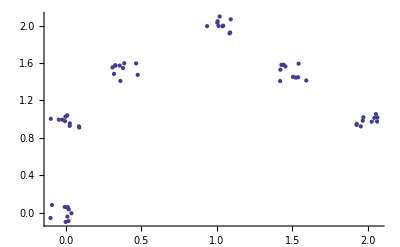

```mathematica
ListPlot[inData]
```

## Zpracování dat neuronovou sítí

Samoorganizující se neuronovou síť použijeme k hledání shluků ve vygenerovaných datech. Vytvoříme síť o šesti neuronech, kterou necháme na datech naučit. Po naučení sítě chceme aby ideálně každý neuron reprezentoval jeden shluk ve vstupních datech. Poté je možné spočítat hraničnípřímky mezi jednotlivými neurony a tím de facto rozdělit do požadovaného počtu shluků celý vstupní prostor.

### Náhodně inicializovaná síť

Nejprve vytvoříme neuronovou síť o šesti neuronech. Počet neuronů určuje kolik shluků se síť pokusí v datech najít.

```mathematica
unsup=InitializeUnsupervisedNet[inData,6];
```

Tuto neuronovou síť naučíme na našich datech

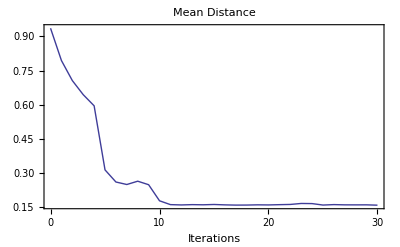

UnsupervisedNet::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{unsup,fitrecord}=UnsupervisedNetFit[inData,unsup,30,ReportFrequency->1];
```

Vidíme že během učení sítě jeden z neuronů “zemřel”, tzn. není použit k rozlišení shluků v datech. Později se mu ještě budeme věnovat.

Ilustraci jaým způsobem byla data rozdělena do shluků nám poskytne následující graf. Pozice neuronu, který reprezentuje daný shluk je naznačena tučným číslem. Je také jasně vidět, který neuron je “mrtvý” a nepřináší nám žádný užitek.

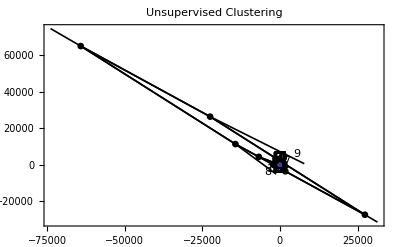

```mathematica
NetPlot[unsup,inData,CbvSymbol->{FontSize->30}]
```

Můžeme také jednoduše nechat “oklasifikovat” nový vektor (zadáme jeho x a y souřadnici).

```mathematica
unsup[{0.2,0.7}]
```

{5}

Číslo, které nám síť vrátila znamená číselné označení shluku, kam vektor spadá (odpovídá číslům v grafu)

Nyní si vzpomeneme, že máme v síti nepotřebný neuron, budeme ho tedy chtít odstranit.
Nejdříve zjistíme o který neuron se jedná.

```mathematica
UnUsedNeurons[unsup,inData]
```

{1}

A poté ho odstraníme. Novou síť bez nepotřebného neuronu pojmenujeme unsup1.

```mathematica
unsup1=NeuronDelete[unsup,%]
```

UnsupervisedNet[{-Codebook Vectors-},{CreationDate → {2011, 5, 4, 0, 0, 27.7752703}, AccumulatedIterations → 30, SOM → None}]

Podíváme se jakým způsobem odděluje síť jednotlivé shluky po odebrání nepotřebného neuronu.

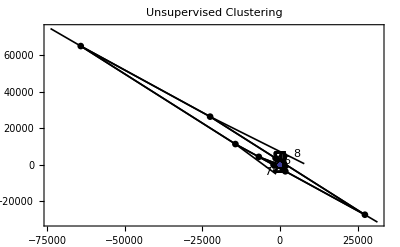

```mathematica
NetPlot[unsup1,inData,CbvSymbol->{FontSize->30}]
```

### Síť inicializovaná metodou SOM

Protože vidíme, že rozdělení dat na shluky ještě není perfektní můžeme se pokust dosáhnout ještě lepšího rozdělení. Místo náhodné inicializace sítě můžeme použít SOM (samoorganizující mapu) k inicializaci sítě. Samoorganizující mapa se nechá přizpůsobit datům, na souřadnicích, kde skončí její neurony, jsou inicializovány neurony naší požadované sítě (naše síť není SOM).

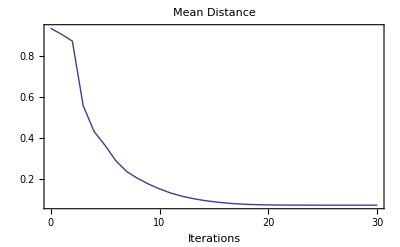

```mathematica
unsup2=InitializeUnsupervisedNet[inData,6,UseSOM ->True,CriterionPlot->True,CriterionLog->True,Iterations->30];
```

Nyní naučíme zinicializovanou síť na našich datech.

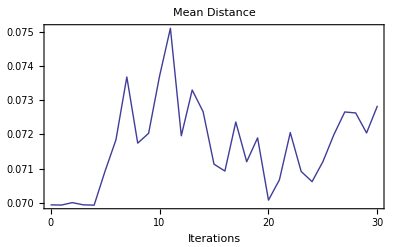

```mathematica
{unsup2,fitrecord2}=UnsupervisedNetFit[inData,unsup2,30];
```

A podíváme se jakým způsobem uřčuje shluky v datech.

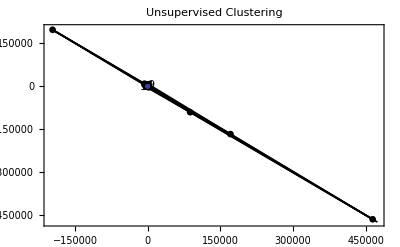

```mathematica
NetPlot[unsup2,inData]
```

Tento přístup k inicializaci sítě nám může často pomoci dosáhnout lepších výsledků, než náhodná inicializace. Také často zabrání problému s “mrtvými” neurony.

## Průběh učení

### Náhodně inicializovaná síť

Ještě se můžeme podívat jak síť v průběhu učení dělila data do shluků a jak se měnila poloha jednotlivých neuronů. Barevné čáry ukazují pohyb jednotlivých neuronů, čísla ukazují jejich konečnou polohu.

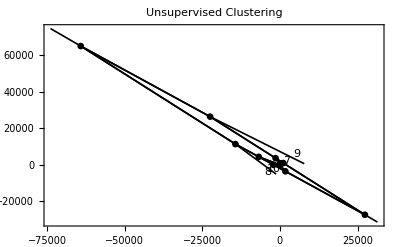

```mathematica
NetPlot[fitrecord,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState=NetPlot[fitrecord,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

### Síť inicializovaná metodou SOM

Z následujícího grafu je patrné, že i pouze zinicializovaná síť metodou SOM by poskytovala poměrně dobré výsledky a její učení upravuje pouze pozici několika neuronů.

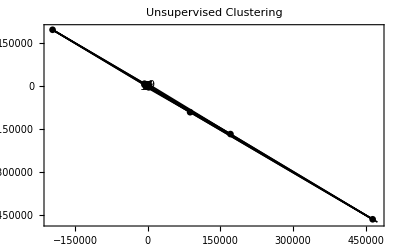

```mathematica
NetPlot[fitrecord2,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState2=NetPlot[fitrecord2,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState2[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.